```mathematica
"ϕ==> Rotate"
"θ==> Tilt"
"ψ==>Twist"
"χ_(i, j, k)^(2)==>Laboratory Coordination, λ(x,y,z)"
"χ_(l, m, n)^(2)==>Molecular Coordination, η(a,b,c)"
```

```mathematica
"From C∞V Character Table"
```

```mathematica
"β_(a, a, c)==A_1 ⊗ A_1==A_1,   Symmetric"
"β_(b, b, c)==A_1 ⊗ A_1==A_1,   Symmetric"
"β_(c, c, C)==A_1 ⊗ A_1==A_1,   Symmetric"
```

```mathematica
x=a=1
y=b=2
z=c=3
```

1

2

3

```mathematica
"Non-zero Microscopic Hyperpolarizability"
```

```mathematica
"Symmetric"
Subscript[β, b,b,c]=Subscript[β, a,a,c]
Subscript[β, c,c,c]
```

Symmetric

β_(1,1,3)

β_(3,3,3)

```mathematica
"Zero Microscopic Hyperpolarizability"
```

```mathematica
Subscript[β, a,a,a]=Subscript[β, a,a,b]=Subscript[β, a,b,a]=Subscript[β, a,b,b]=Subscript[β, a,b,c]=Subscript[β, a,c,a]=Subscript[β, a,c,b]=Subscript[β, a,c,c]=0
Subscript[β, b,a,a]=Subscript[β, b,a,b]=Subscript[β, b,a,c]=Subscript[β, b,b,a]=Subscript[β, b,b,b]=Subscript[β, b,c,a]=Subscript[β, b,c,b]=Subscript[β, b,c,c]=0
Subscript[β, c,a,a]=Subscript[β, c,a,b]=Subscript[β, c,a,c]=Subscript[β, c,b,a]=Subscript[β, c,b,b]=Subscript[β, c,b,c]=Subscript[β, c,c,a]=Subscript[β, c,c,b]=0
```

0

0

0

```mathematica
"Euler Transformation Matrix"
```

```mathematica
ℝ=({{Cos[ψ]Cos[ϕ]-Cos[θ]Sin[ϕ]Sin[ψ], -Sin[ψ]Cos[ϕ]-Cos[θ]Sin[ϕ]Cos[ψ], Sin[θ]Sin[ϕ]}, {Cos[ψ]Sin[ϕ]+Cos[θ]Cos[ϕ]Sin[ψ], -Sin[ψ]Sin[ϕ]+Cos[θ]Cos[ϕ]Cos[ψ], -Sin[θ]Cos[ϕ]}, {Sin[θ]Sin[ψ], Sin[θ]Cos[ψ], Cos[θ]}})
```

{{Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ],-Cos[θ] Cos[ψ] Sin[ϕ]-Cos[ϕ] Sin[ψ],Sin[θ] Sin[ϕ]},{Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ],Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ],-Cos[ϕ] Sin[θ]},{Sin[θ] Sin[ψ],Cos[ψ] Sin[θ],Cos[θ]}}

```mathematica
"For SSP"
```

```mathematica
Subscript[χ, i, j, k]=∑_(l=a)^c ∑_(m=a)^c ∑_(n=a)^c   ℝ[[i,l]] ℝ[[j,m]] ℝ[[k,n]] Subscript[β, l ,m ,n]/.{i->y,j->y,k->z}
```

Part::pspec: Part specification i is neither an integer nor a list of integers.

Part::pspec: Part specification j is neither an integer nor a list of integers.

Part::pspec: Part specification k is neither an integer nor a list of integers.

General::stop: Further output of Part will be suppressed during this calculation.

Cos[θ] (Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ])^2 β_(1,1,3)+Cos[θ] (Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ])^2 β_(1,1,3)+Cos[θ] Cos[ϕ]^2 Sin[θ]^2 β_(3,3,3)

```mathematica
"SSP Symmetric Stretching-->β_(a, a, c) , β_(c, c, c)"
```

```mathematica
Subscript[χ, y,y,z]^((2)ss)=
Expand[Cos[θ] (Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ])^2 Subscript[β, a,a,c]+Cos[θ] (Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ])^2 Subscript[β, a,a,c]+Cos[θ] Cos[ϕ]^2 Sin[θ]^2 Subscript[β, c,c,c]]

=Cos[θ] Sin[ϕ]^2 Cos[ψ]^2 Subscript[β, a,a,c]+Cos[θ] Sin[ϕ]^2 Sin[ψ]^2 Subscript[β, a,a,c]+Cos[θ]^3 Cos[ϕ]^2 Cos[ψ]^2 Subscript[β, a,a,c]+Cos[θ]^3 Cos[ϕ]^2 Sin[ψ]^2 Subscript[β, a,a,c]+Cos[θ] Cos[ϕ]^2 Sin[θ]^2 Subscript[β, c,c,c]

=Cos[θ] Sin[ϕ]^2(Cos[ψ]^2+Sin[ψ]^2)Subscript[β, a,a,c]+Cos[θ]^3 Cos[ϕ]^2(Cos[ψ]^2+Sin[ψ]^2)Subscript[β, a,a,c]+Cos[θ] Cos[ϕ]^2 Sin[θ]^2 Subscript[β, c,c,c]

=Cos[θ] Sin[ϕ]^2 Subscript[β, a,a,c]+Cos[θ]^3 Cos[ϕ]^2 Subscript[β, a,a,c]+Cos[θ] Cos[ϕ]^2 Sin[θ]^2 Subscript[β, c,c,c]

=Cos[θ] Sin[ϕ]^2 Subscript[β, a,a,c]+Cos[θ]^3 Cos[ϕ]^2 Subscript[β, a,a,c]+Cos[θ] Sin[ϕ]^2 Subscript[β, a,a,c]+ Cos[θ] Cos[ϕ]^2 (1-Cos[θ]^2)Subscript[β, c,c,c]

=Cos[θ] Sin[ϕ]^2 Subscript[β, a,a,c]+Cos[θ]^3 Cos[ϕ]^2 Subscript[β, a,a,c]+ Cos[θ] Cos[ϕ]^2 Subscript[β, c,c,c]-Cos[θ]^3 Cos[ϕ]^2 Subscript[β, c,c,c]

=(Cos[ϕ]^2 Subscript[β, c,c,c]+Sin[ϕ]^2 Subscript[β, a,a,c])Cos[θ]-(Subscript[β, c,c,c]-Subscript[β, a,a,c])Cos[θ]^3 Cos[ϕ]^2

=Subscript[β, c,c,c]((Cos[ϕ]^2+Sin[ϕ]^2 Subscript[β, a,a,c]/Subscript[β, c,c,c])Cos[θ]-(1-Subscript[β, a,a,c]/Subscript[β, c,c,c])Cos[θ]^3 Cos[ϕ]^2)
```

```mathematica
R=Subscript[β, a,a,c]/Subscript[β, c,c,c]

Subscript[χ, y,y,z]^((2)ss)=Subscript[β, c,c,c] Cos[ϕ]^2((1+(Sin[ϕ]/Cos[ϕ])^2 R)Cos[θ]-(1-R)Cos[θ]^3)
```

```mathematica
"Average Over Orientation (ϕ)"
```

```mathematica
Subscript[Ν, s]/(2π)(∫_0^(2π) (Subscript[β, c,c,c] Cos[ϕ]^2((1+(Sin[ϕ]/Cos[ϕ])^2 R)Cos[θ]-(1-R)Cos[θ]^3))ⅆϕ)

=1/2 Cos[θ] (1+R+(-1+R) Cos[θ]^2) Subscript[Ν, s] Subscript[β, c,c,c]
```

```mathematica
Subscript[χ, y,y,z]^((2)ss)=1/2 Subscript[Ν, s] Subscript[β, c,c,c]((1+R)Cos[θ]-(1-R)Cos[θ]^3)
```

```mathematica
"Plot"
```

```mathematica
Subscript[Ν, s]=1
Subscript[β, c,c,c]=1
R=0.5
```

1

1

0.5

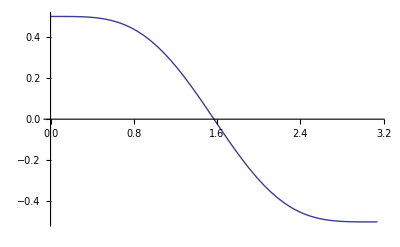

```mathematica
Plot[1/2 Subscript[Ν, s] Subscript[β, c,c,c]((1+R)Cos[θ]-(1-R)Cos[θ]^3),{θ,0Degree, 180 Degree}]
```